```mathematica
Quit[]
```

# General

```mathematica
(*knowns:{R,d}*)
```

```mathematica
$Assumptions=x>0&&d>0&&R>0&&Element[α,Reals]&&α>0;
```

```mathematica
fullsolφ0= {Cos[φ0]->√(1-R^2/d^2),Sin[φ0]-> R/d,φ0-> ArcSin[R/d]};
angsimp={Sin[θ-ϕ-φ0]-> (Cos[φ0] Sin[θ-ϕ]-Cos[θ-ϕ] Sin[φ0]),Sin[θ-ϕ+φ0]-> (Cos[φ0] Sin[θ-ϕ]+Cos[θ-ϕ] Sin[φ0])};
```

```mathematica
α1[θ_,ϕ_] = Pi/2- ϕ +θ + φ0;
α2[θ_,ϕ_]= Pi/2- ϕ +θ - φ0;
r1[θ_,ϕ_,x_]= Sqrt[d^2 + x^2- 2 d x Cos[α1[θ,ϕ]]];
r2[θ_,ϕ_,x_]= Sqrt[d^2 + x^2- 2 d x Cos[α2[θ,ϕ]]];
Rimg[rcirc_,θ_,ϕ_,x_]=FullSimplify[(rcirc Sqrt[(-(r1[θ,ϕ,x]^2 + r2[θ,ϕ,x]^2 - 4 R^2)/(2r1[θ,ϕ,x] r2[θ,ϕ,x])+1)/2]/.angsimp)/.fullsolφ0];(*,Assumptions->x>0&&d>0&&R>0]*)
φimg[θ_,ϕ_,x_]=ArcCos[(r1[θ,ϕ,x] ^2+ r2[θ,ϕ,x]^2 - 4 R^2)/(2 r1[θ,ϕ,x] r2[θ,ϕ,x])]/2//FullSimplify;
θ0[θ_,ϕ_,x_]=ArcCos[(r1[θ,ϕ,x] ^2+ d^2 -  x^2)/(2 r1[θ,ϕ,x] d)]//FullSimplify;
θimg [θ_,ϕ_,x_]=(θ + φ0-φimg[θ,ϕ,x]+(-1)^Quotient[ϕ-φ0-θ+Pi/2,Pi]θ0[θ,ϕ,x]/.angsimp)/.fullsolφ0//FullSimplify
Ω[θ_,ϕ_,x_]=(2Pi(1- Sqrt[(1+(r1[θ,ϕ,x]^2 + r2[θ,ϕ,x]^2 - (2R)^2)/(2 r1[θ,ϕ,x] r2[θ,ϕ,x]))/2])/.angsimp)/.fullsolφ0//FullSimplify;
```

θ+(-1)^Quotient[-θ+ϕ+ArcCos[R/d],π] ArcCos[(d^2+R x Cos[θ-ϕ]+√((d-R) (d+R)) x Sin[θ-ϕ])/(d √(d^2+x^2+2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ]))]-1/2 ArcCos[(d^2-2 R^2+x^2+2 √((d-R) (d+R)) x Sin[θ-ϕ])/(√(d^2+x^2-2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ]) √(d^2+x^2+2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ]))]+ArcSin[R/d]

```mathematica
Ω[3Pi/6,Pi/4,1]/.{R-> 1,d-> 6.5}//N
```

0.0597632

# Detetor 1

```mathematica
r1det1 Sqrt[(1-(r1det1^2 + r2det1^2 - 4 R^2)/(2 r1det1 r2det1))/2]//FullSimplify
```

1/2 r1det1 √((4 R^2-(r1det1-r2det1)^2)/(r1det1 r2det1))

```mathematica
α1det1 = α1[θ,ϕ]
α2det1= α2[θ,ϕ]
r1det1= r1[θ,ϕ,x]
r2det1= r2[θ,ϕ,x]
Rimgdet1=(Rimg[r1det1,θ,ϕ,x]/.angsimp)/.fullsolφ0//FullSimplify
```

π/2+θ-ϕ+φ0

π/2+θ-ϕ-φ0

√(d^2+x^2+2 d x Sin[θ-ϕ+φ0])

√(d^2+x^2+2 d x Sin[θ-ϕ-φ0])

√(1/2 (d^2+x^2)+R x Cos[θ-ϕ]+√((d-R) (d+R)) x Sin[θ-ϕ]) √(1-(d^2-2 R^2+x^2+2 √((d-R) (d+R)) x Sin[θ-ϕ])/(√(d^2+x^2-2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ]) √(d^2+x^2+2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ])))

```mathematica
FullSimplify[Series[Rimgdet1,{x,0,1}]]//Normal
```

R+(R^2 x Cos[θ-ϕ])/d^2

```mathematica
Ωdet1=Ω[θ,ϕ,x]
```

-π (-2+√(2+(2 (d^2-2 R^2+x^2+2 √((d-R) (d+R)) x Sin[θ-ϕ]))/(√(d^2+x^2-2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ]) √(d^2+x^2+2 R x Cos[θ-ϕ]+2 √((d-R) (d+R)) x Sin[θ-ϕ]))))

```mathematica
(*α = R/d*)
```

```mathematica
Collect[Series[(Series[Ωdet1,{x,0,1}]//FullSimplify)/.{R->d Sqrt[ Ω0/Pi]},{ Ω0,0,1}], Ω0,FullSimplify]
```

Ω0 (1-(2 x Sin[θ-ϕ])/d)

```mathematica
Series[Ω0 d^2/(d+x)^2,{x,0,1}]
```

Ω0-(2 Ω0 x)/d+O[x]^2

```mathematica
θimg0det1=θimg[θ,ϕ,x];
```

# Detetor 2

```mathematica
α1det2 = α1[Pi,ϕ]
α2det2= α2[Pi,ϕ]
r1det2= r1[Pi,ϕ,x]
r2det2= r2[Pi,ϕ,x]
Rimgdet2=(Rimg[r1det1,Pi,ϕ,x]/.angsimp)/.fullsolφ0//FullSimplify
```

(3 π)/2-ϕ+φ0

(3 π)/2-ϕ-φ0

√(d^2+x^2+2 d x Sin[ϕ-φ0])

√(d^2+x^2+2 d x Sin[ϕ+φ0])

√(1/2 (d^2+x^2)+R x Cos[θ-ϕ]+√((d-R) (d+R)) x Sin[θ-ϕ]) √(1-(d^2-2 R^2+x^2+2 √((d-R) (d+R)) x Sin[ϕ])/(√(d^2+x^2-2 R x Cos[ϕ]+2 √((d-R) (d+R)) x Sin[ϕ]) √(d^2+x^2+2 R x Cos[ϕ]+2 √((d-R) (d+R)) x Sin[ϕ])))

```mathematica
Ωdet2=Ω[Pi,ϕ,x]
```

-π (-2+√(2+(2 (d^2-2 R^2+x^2+2 √((d-R) (d+R)) x Sin[ϕ]))/(√(d^2+x^2-2 R x Cos[ϕ]+2 √((d-R) (d+R)) x Sin[ϕ]) √(d^2+x^2+2 R x Cos[ϕ]+2 √((d-R) (d+R)) x Sin[ϕ]))))

```mathematica
(*α = R/d*)
```

```mathematica
θimg0det2=θimg[Pi,ϕ,x]-Pi;
```

# Intersection

```mathematica
Δl0=(r1det1 Sin[(θimg0det1-θimg0det2)]/.angsimp)/.fullsolφ0;
```

```mathematica
A[R1_,R2_,l_]=If[l<R1+R2,If[Abs[l]<Abs[R2-R1],If[R2<R1,Pi R2^2, Pi R1^2],R2^2 ArcCos[(l^2+R2^2-R1^2)/(2l R2)]+R1^2 ArcCos[(l^2+R1^2-R2^2)/(2l R1)]-Sqrt[(-l+R2+R1)(l+R2-R1)(l-R2+R1)(l+R2+R1)]/2],0];
```

```mathematica
GenExp=(A[Rimgdet1,Rimgdet2,Abs[Δl0]]/r1det1^2/. angsimp)/.fullsolφ0;
```

# Plots

```mathematica
GenExp/. {ϕ->Pi/2,θ-> -Pi/24,d-> 15,R-> 2,x->1}// N
```

0.0205829

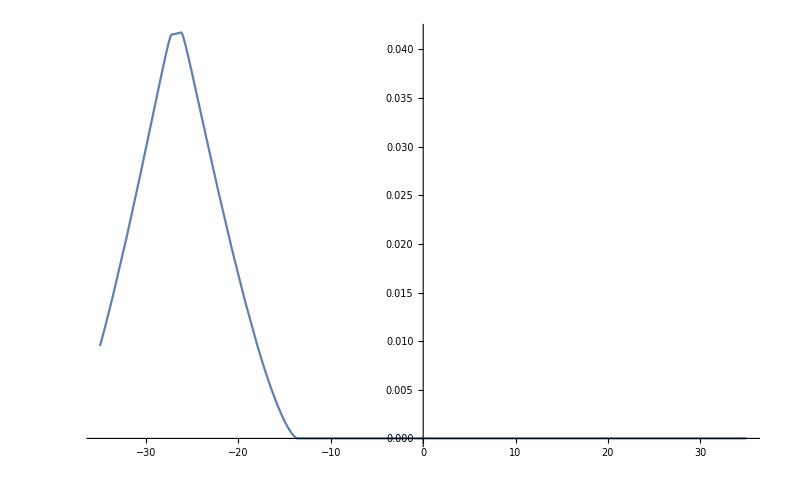

```mathematica
Plot[GenExp/. {ϕ->0,d-> 15,R-> 2,x->-3.8,θ-> Pi/180 θgrad},{θgrad,-35,35}]
```

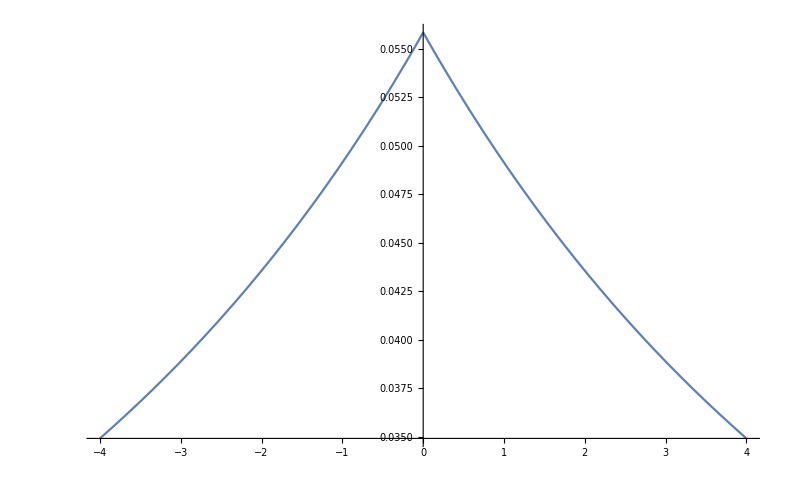

```mathematica
Plot[If[xeq> 0,GenExp/. {ϕ->Pi/2,d-> 15,R-> 2,θ-> 0,x-> xeq},GenExp/. {ϕ->-Pi/2,d-> 15,R-> 2,θ-> 0,x-> -xeq}],{xeq,-4,4}]
```

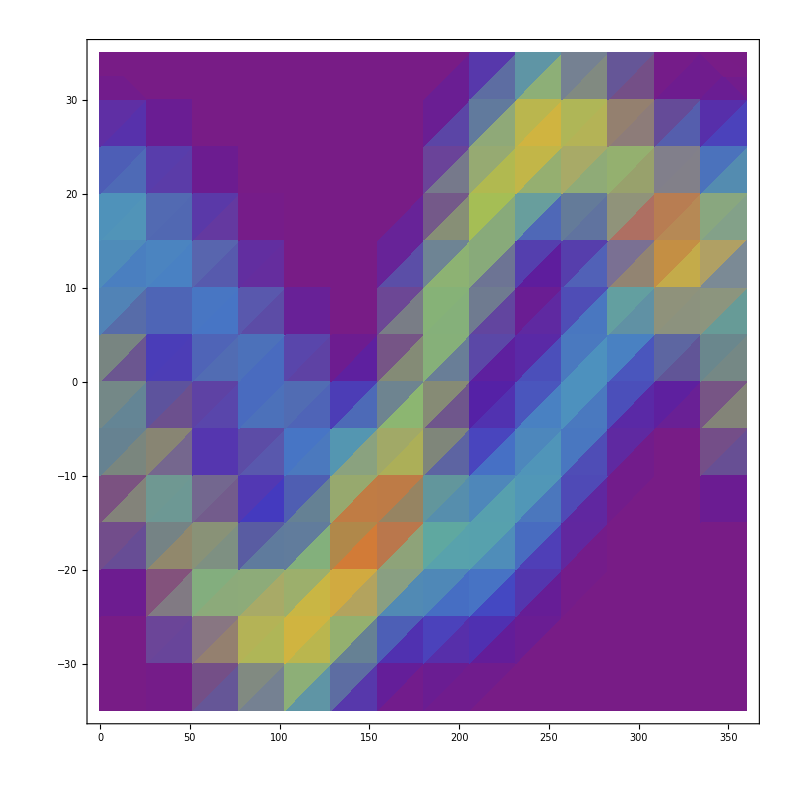

```mathematica
DensityPlot[2/3(GenExp/. {d-> 16,R-> 2,x->3.81,θ-> -Pi/180 θgrad,ϕ-> Pi/180 (ϕgrad+90)} )+1/3( GenExp/. {d-> 16,R-> 2,x->2.54,θ-> -Pi/180 θgrad,ϕ-> Pi/180 (ϕgrad)}),{ϕgrad,0,360},{θgrad,-35,35},ColorFunction->"Rainbow"]
```